```mathematica
2変数の回帰分析
```

2 変数の回帰分析

```mathematica
⓪データの用意;
```

```mathematica
元データ={{10,8,8,5,7,8,7,9,6,9},{80,0,200,200,300,230,40,0,330,180},{469,366,371,208,246,297,363,436,198,364}};
元データ//MatrixForm
```

(10 | 8 | 8 | 5 | 7 | 8 | 7 | 9 | 6 | 9
80 | 0 | 200 | 200 | 300 | 230 | 40 | 0 | 330 | 180
469 | 366 | 371 | 208 | 246 | 297 | 363 | 436 | 198 | 364)

```mathematica
お店の面積(*坪*)=元データ[[1]];
```

```mathematica
最寄り駅からの距離(*m*)=元データ[[2]];
```

```mathematica
売り上げ(*万円*)=元データ[[3]];
```

```mathematica
各お店のデータ=Transpose[元データ]
各お店のデータ//MatrixForm
```

{{10,80,469},{8,0,366},{8,200,371},{5,200,208},{7,300,246},{8,230,297},{7,40,363},{9,0,436},{6,330,198},{9,180,364}}

(10 | 80 | 469
8 | 0 | 366
8 | 200 | 371
5 | 200 | 208
7 | 300 | 246
8 | 230 | 297
7 | 40 | 363
9 | 0 | 436
6 | 330 | 198
9 | 180 | 364)

```mathematica
p0=ListPointPlot3D[各お店のデータ,PlotStyle->Black,AxesLabel->{"面積(坪)","駅からの距離(m)","店ごとの売り上げ(万円)"},LabelStyle->12]
```

-Graphics3D-

```mathematica
a//Clear
```

```mathematica
①お店の面積と売り上げの相関を調べる;
```

```mathematica
面積と売り上げデータ=Transpose[List[お店の面積,売り上げ]];
面積と売り上げデータ//MatrixForm
```

(10 | 469
8 | 366
8 | 371
5 | 208
7 | 246
8 | 297
7 | 363
9 | 436
6 | 198
9 | 364)

```mathematica
予測= b + a x;
```

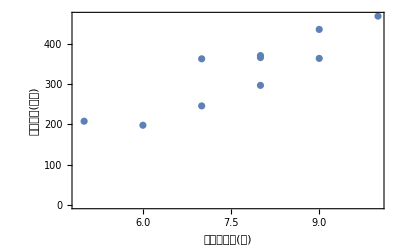

```mathematica
p1=ListPlot[面積と売り上げデータ,Frame->True,FrameLabel->{"お店の面積(坪)","売り上げ(万円)"},FrameStyle->16]
```

```mathematica
面積と売り上げ予測から求めたパラメータ=FindFit[面積と売り上げデータ,予測,{a,b},x]
```

{a→54.9453,b→-91.2786}

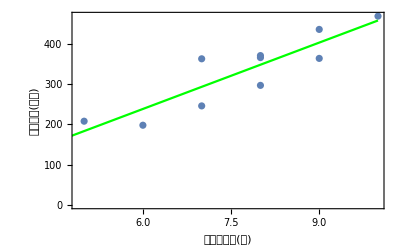

```mathematica
Show[p1,
Plot[{予測/.面積と売り上げ予測から求めたパラメータ},{x,0,10},PlotStyle->Green]
]
```

```mathematica
②最寄り駅からの距離と売り上げの相関を調べる;
```

```mathematica
駅からの距離と売り上げデータ=Transpose[List[最寄り駅からの距離,売り上げ]];
駅からの距離と売り上げデータ//MatrixForm
```

(80 | 469
0 | 366
200 | 371
200 | 208
300 | 246
230 | 297
40 | 363
0 | 436
330 | 198
180 | 364)

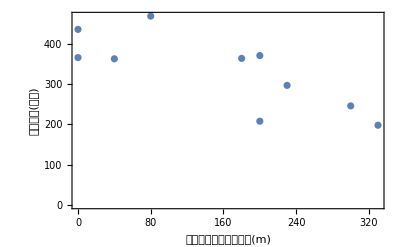

```mathematica
p2=ListPlot[駅からの距離と売り上げデータ,Frame->True,FrameLabel->{"最寄りの駅からの距離(m)","売り上げ(万円)"},FrameStyle->16]
```

```mathematica
駅からの距離と売り上げ予測から求めたパラメータ=FindFit[駅からの距離と売り上げデータ,予測,{a,b},x]
```

{a→-0.596073,b→424.787}

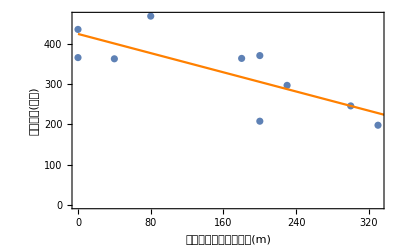

```mathematica
Show[p2,
Plot[{予測/.駅からの距離と売り上げ予測から求めたパラメータ},{x,0,350},PlotStyle->Orange]
]
```

```mathematica
③2変数で最小二乗法;
```

```mathematica
Clear[a]
Clear[b]
```

```mathematica
２変数のモデル= β0+ β1 x1+β2 x2
```

β0+x1 β1+x2 β2

```mathematica
FindFit[各お店のデータ,２変数のモデル,{β0,β1,β2},{x1,x2}]
```

{β0→65.3239,β1→41.5135,β2→-0.340883}

```mathematica
残差平方和[β0_,β1_,β2_]:=Total[(売り上げ-(β0+ β1 お店の面積+β2 最寄り駅からの距離))^2]
```

```mathematica
最適パラメータ=NSolve[{D[残差平方和[β0,β1,β2],β0]==0,D[残差平方和[β0,β1,β2],β1]==0,D[残差平方和[β0,β1,β2],β2]==0},{β0,β1,β2}]
```

{{β0→65.3239,β1→41.5135,β2→-0.340883}}

```mathematica
Plot3D[２変数のモデル/.最適パラメータ,{x1,0,10},{x2,0,350}]
```

-Graphics3D-

```mathematica
Show[p0,Plot3D[２変数のモデル/.最適パラメータ,{x1,0,10},{x2,0,350},PlotStyle->Opacity[0.1]]]
```

-Graphics3D-

```mathematica
④標本化を行う;
面積平均=Mean[お店の面積]//N
```

7.7

```mathematica
お店の面積標準化ver=(お店の面積-面積平均)/StandardDeviation[お店の面積]
```

{1.53904,0.200745,0.200745,-1.8067,-0.468405,0.200745,-0.468405,0.869894,-1.13755,0.869894}

```mathematica
距離平均=Mean[最寄り駅からの距離]//N
```

156.

```mathematica
駅からの距離標準化ver=(最寄り駅からの距離-距離平均)/StandardDeviation[最寄り駅からの距離]
```

{-0.635199,-1.30383,0.367747,0.367747,1.20353,0.618483,-0.969514,-1.30383,1.45427,0.200589}

```mathematica
売上平均=Mean[売り上げ]//N
```

331.8

```mathematica
売上標準化ver=(売り上げ-売上平均)/StandardDeviation[売り上げ]
```

{1.49107,0.371682,0.426021,-1.34544,-0.932464,-0.378202,0.339078,1.13243,-1.45412,0.349946}

```mathematica
標準化データ=Transpose[{お店の面積標準化ver,駅からの距離標準化ver,売上標準化ver}];
標準化データ//MatrixForm
```

(1.53904 | -0.635199 | 1.49107
0.200745 | -1.30383 | 0.371682
0.200745 | 0.367747 | 0.426021
-1.8067 | 0.367747 | -1.34544
-0.468405 | 1.20353 | -0.932464
0.200745 | 0.618483 | -0.378202
-0.468405 | -0.969514 | 0.339078
0.869894 | -1.30383 | 1.13243
-1.13755 | 1.45427 | -1.45412
0.869894 | 0.200589 | 0.349946)

```mathematica
p3=ListPointPlot3D[標準化データ,PlotStyle->Black,AxesLabel->{"標準化面積","標準化距離","標準化売上"},LabelStyle->12,BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
FindFit[標準化データ,２変数のモデル,{β0,β1,β2},{x1,x2}]
```

{β0→-5.35709×10^-17,β1→0.674234,β2→-0.443255}

```mathematica
残差平方和2[β0_,β1_,β2_]:=Total[(売上標準化ver-(β0+ β1 お店の面積標準化ver+β2 駅からの距離標準化ver))^2]
```

```mathematica
最適パラメータ2=NSolve[{D[残差平方和2[β0,β1,β2],β0]==0,D[残差平方和2[β0,β1,β2],β1]==0,D[残差平方和2[β0,β1,β2],β2]==0},{β0,β1,β2}]
```

{{β0→-4.34007×10^-17,β1→0.674234,β2→-0.443255}}

```mathematica
Plot3D[２変数のモデル/.最適パラメータ2,{x1,-1.6,1.6},{x2,-1.6,1.6}];
```

```mathematica
Show[p3,Plot3D[２変数のモデル/.最適パラメータ2,{x1,-1.6,1.6},{x2,-1.6,1.6},PlotStyle->Opacity[0.1]]]
```

-Graphics3D-

#### ⑤X^T xとは？;

```mathematica
元データ
```

{{10,8,8,5,7,8,7,9,6,9},{80,0,200,200,300,230,40,0,330,180},{469,366,371,208,246,297,363,436,198,364}}

```mathematica
Drop[元データ,-1]
```

{{10,8,8,5,7,8,7,9,6,9},{80,0,200,200,300,230,40,0,330,180}}

```mathematica
Table[1,10]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
xt=Prepend[Drop[元データ,-1],Table[1,10]]
```

{{1,1,1,1,1,1,1,1,1,1},{10,8,8,5,7,8,7,9,6,9},{80,0,200,200,300,230,40,0,330,180}}

```mathematica
xt//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
10 | 8 | 8 | 5 | 7 | 8 | 7 | 9 | 6 | 9
80 | 0 | 200 | 200 | 300 | 230 | 40 | 0 | 330 | 180)

```mathematica
x=Transpose[xt];
x//MatrixForm
```

(1 | 10 | 80
1 | 8 | 0
1 | 8 | 200
1 | 5 | 200
1 | 7 | 300
1 | 8 | 230
1 | 7 | 40
1 | 9 | 0
1 | 6 | 330
1 | 9 | 180)

```mathematica
xt.x//MatrixForm
```

(10 | 77 | 1560
77 | 613 | 11220
1560 | 11220 | 372200)

```mathematica
N[xt.x/10]//MatrixForm
```

(1. | 7.7 | 156.
7.7 | 61.3 | 1122.
156. | 1122. | 37220.)

```mathematica
({{1, OverBar[Subscript[x, 1]], OverBar[Subscript[x, 2]]}, {OverBar[Subscript[x, 1]], OverBar[Subscript[x, 1]]^2+Subscript[σ, 1]^2, OverBar[Subscript[x, 1]] OverBar[Subscript[x, 2]]+Subscript[σ, 12]}, {OverBar[Subscript[x, 2]], OverBar[Subscript[x, 1]] OverBar[Subscript[x, 2]]+Subscript[σ, 12], OverBar[Subscript[x, 2]]^2+Subscript[σ, 2]^2}});
```

```mathematica
⑥分散と共分散;
```

```mathematica
○OverBar[Subscript[x, 1]]->[1,2]成分、[2,1]成分
```

```mathematica
お店の面積平均=Mean[お店の面積]//N
```

7.7

```mathematica
○OverBar[Subscript[x, 2]]->[1,3]成分、[3,1]成分
```

```mathematica
最寄り駅からの距離平均=Mean[最寄り駅からの距離]//N
```

156.

```mathematica
○OverBar[Subscript[x, 1]]^2+Subscript[σ, 1]^2->[2,2]成分
```

```mathematica
お店の面積分散=Variance[お店の面積]//N
```

2.23333

```mathematica
(お店の面積平均)^2
```

59.29

```mathematica
お店の面積分散+(お店の面積平均)^2(*行列の計算とは少し値が違う値が出た*)
```

61.5233

```mathematica
1/(Length[お店の面積]-1)Total[(お店の面積-お店の面積平均)^2]
```

2.23333

```mathematica
1/Length[お店の面積] Total[(お店の面積-お店の面積平均)^2]
```

2.01

```mathematica
1/Length[お店の面積] Total[(お店の面積-お店の面積平均)^2]+(お店の面積平均)^2(*行列計算では不偏分散ではなく、標本分散である*)
```

61.3

```mathematica
○OverBar[Subscript[x, 2]]^2+Subscript[σ, 2]^2->[3,3]成分
```

```mathematica
最寄り駅からの距離分散=Variance[最寄り駅からの距離]//N
```

14315.6

```mathematica
(最寄り駅からの距離平均)^2
```

24336.

```mathematica
最寄り駅からの距離分散+(最寄り駅からの距離平均)^2
```

38651.6

```mathematica
1/Length[最寄り駅からの距離] Total[(最寄り駅からの距離-最寄り駅からの距離平均)^2]+(最寄り駅からの距離平均)^2
```

37220.

```mathematica
○OverBar[Subscript[x, 1]] OverBar[Subscript[x, 2]]+Subscript[σ, 12]->[2,3]成分、[3,2]成分
```

```mathematica
Covariance[お店の面積,最寄り駅からの距離]
```

-88

```mathematica
お店の面積平均*最寄り駅からの距離平均
```

1201.2

```mathematica
お店の面積平均*最寄り駅からの距離平均+Covariance[お店の面積,最寄り駅からの距離](*不偏共分散で計算しているからだろう、、、*)
```

1113.2

```mathematica
お店の面積平均*最寄り駅からの距離平均+1/Length[お店の面積] Total[(お店の面積-お店の面積平均)*(最寄り駅からの距離-最寄り駅からの距離平均)](*行列での計算結果が標本共分散であることがわかった*)
```

1122.

```mathematica
⑦相関係数;
```

```mathematica
r12=Covariance[お店の面積,最寄り駅からの距離]/(StandardDeviation[お店の面積] StandardDeviation[最寄り駅からの距離])//N(*面積と距離の相関係数*)
```

-0.492155

```mathematica
r13=Covariance[お店の面積,売り上げ]/(StandardDeviation[お店の面積]StandardDeviation[売り上げ])　//N(*面積と売上の相関係数*)
```

0.892385

```mathematica
r23=Covariance[最寄り駅からの距離,売り上げ]/(StandardDeviation[最寄り駅からの距離] StandardDeviation[売り上げ])//N(*距離と売上の相関係数*)
```

-0.775083

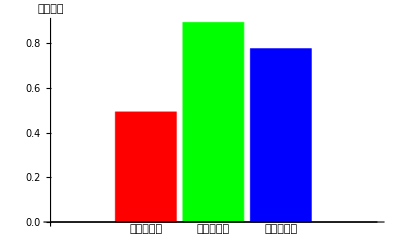

```mathematica
BarChart[{r12//Abs,r13//Abs,r23//Abs},ChartStyle->{Red,Green,Blue},AxesLabel->"相関係数" ,ChartLabels->{"面積と距離","面積と売上","距離と売上"}]
```

```mathematica
-Graphics-;
```

```mathematica
r123=(r12-r13 r23)/(√(1-r13^2) √(1-r23^2))(*面積と距離の偏相関係数*)
```

0.699709

```mathematica
r132=(r13-r12 r23)/(√(1-r12^2) √(1-r23^2))(*面積と売上の偏相関係数*)
```

0.928887

```mathematica
r231=(r23-r12 r13)/(√(1-r12^2) √(1-r13^2))(*距離と売上の偏相関係数*)
```

-0.855036

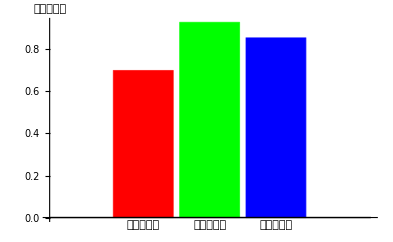

```mathematica
BarChart[{r123//Abs,r132//Abs,r231//Abs},ChartStyle->{Red,Green,Blue},AxesLabel->"偏相関係数" ,ChartLabels->{"面積と距離","面積と売上","距離と売上"}]
```

```mathematica
Covariance[お店の面積,売り上げ]/Variance[お店の面積]//N
```

54.9453

```mathematica
r13 StandardDeviation[売り上げ]/StandardDeviation[お店の面積]
```

54.9453

```mathematica
(Variance[お店の面積] Covariance[お店の面積,売り上げ]-Covariance[お店の面積,最寄り駅からの距離]Covariance[最寄り駅からの距離,売り上げ])/(Variance[お店の面積]Variance[最寄り駅からの距離]-Covariance[お店の面積,最寄り駅からの距離]^2)//N
```

-30.9831

```mathematica
r132 (StandardDeviation[売り上げ] √(1-r23^2))/(StandardDeviation[お店の面積] √(1-r12^2))
```

41.5135

```mathematica
(*偏相関係数を使って偏回帰係数β1を割り出すことができた*)
```